```mathematica
Scan[SetOptions[#1,{Axes->True, Frame->True, FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times"],FrameTicksStyle->Directive[Black, 15], LabelStyle->Directive[14], AspectRatio->1}]&,{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListLinePlot,ListStepPlot,DateListPlot,DateListStepPlot,DateListLogPlot}
];
```

# Working Code

## Modules

#### Load data

Each module returns a list with {coordinates, velocities, LMC tags}.  The modules only different in the source of the data.

```mathematica
getLMCDataHDF5[hdf5filenameSTR_]:=Module[{dmCords00,dmVels00,dmTag00,dmDataMAT},
dmCords00=Import[hdf5filenameSTR, "/Coordinates"] ;
dmVels00=Import[hdf5filenameSTR, "/Velocities"];
dmTag00=Import[hdf5filenameSTR, "/LMC_tag"];
{dmCords00,dmVels00,dmTag00}
]
```

```mathematica
getLMCDataCSV[csvfilenameSTR_]:=Module[{LMCDataMatrix,LMCData,dmCords00,dmVels00,dmTag00,dmDataMAT},
LMCDataMatrix=Import[csvfilenameSTR,"CSV"] ;
LMCData=Rest@LMCDataMatrix;
dmCords00=LMCData⟦All,;;3⟧;
dmVels00=LMCData⟦All,4;;6⟧;
dmTag00=LMCData⟦All,7⟧;
{dmCords00,dmVels00,dmTag00}
]
```

#### Data munging

```mathematica
tblHeadings={"x","y","z","Vx","Vy","Vz","tag","iTag","r","r6to10","r7to9"};
```

```mathematica
buildDataSet[coordinates_,velocities_,lmcTag_]:=Module[{iTagVEC,iTagMAT,lmcTagMAT,rCoordVEC,rCoordMAT,r6to10VEC,r7to9VEC,r6to10MAT,r7to9MAT,LMCDataMAT},
iTagVEC=If[#==-1,"mw","lmc"]&/@lmcTag;
iTagMAT=Partition[iTagVEC,1];
lmcTagMAT=Partition[lmcTag,1];
rCoordVEC=Norm[#]&/@coordinates;
rCoordMAT=Partition[rCoordVEC,1];
r6to10VEC=If[(#≥6.0 &&#≤10),1,0]&/@r;
r7to9VEC=If[(#≥7.0 &&#≤9),1,0]&/@r;
r6to10MAT=Partition[r6to10VEC,1];
r7to9MAT=Partition[r7to9VEC,1];
LMCDataMAT=Join[coordinates,velocities,lmcTagMAT,iTagMAT,rCoordMAT,r6to10MAT,r7to9MAT,2]
]
```

#### Data checks

```mathematica
tallyDMLMC[iTag_]:=Module[{n,iMW,nMW,iLMC,numLMC,LMCperSTR,iTagCountSTR,iTagPercentSTR,iTagCheckReport},
n=Length@iTag;
{{iMW,nMW},{iLMC,numLMC}}=Tally[iTag];
LMCperSTR=ToString[N[(numLMC/n)*100,2]];
iTagCountSTR="The Number of DM LMC particles for dmTag00 is: "<> ToString[numLMC];
iTagPercentSTR="The LMC percent of total is: "<>LMCperSTR ;
iTagCheckReport=iTagCountSTR~~"\n"~~iTagPercentSTR
]
```

#### Check Plots

```mathematica
positionCheck2D[LMCDataSet_]:=Module[{x,y,z,lp1,lp2,lp3,lpARR},
x=LMCDataSet⟦All,1⟧;
y=LMCDataSet⟦All,2⟧;
z=LMCDataSet⟦All,3⟧;
lp1=ListPlot[{x,y}ᵀ,FrameLabel->{"x (kpc)","z (kpc)"},PlotRange->{{-15,15},{-15,15}}];
lp2=ListPlot[{x,z}ᵀ,FrameLabel->{"x (kpc)","z (kpc)"},PlotRange->{{-15,15},{-15,15}}];
lp3=ListPlot[{y,z}ᵀ,FrameLabel->{"y (kpc)","z (kpc)"},PlotRange->{{-15,15},{-15,15}}];
lpARR={lp1,lp2,lp3}
]
```

```mathematica
positionCheck3D[LMCDataSet_]:=Module[{x,y,z,coord3D},
x=LMCDataSet⟦All,1⟧;
y=LMCDataSet⟦All,2⟧;
z=LMCDataSet⟦All,3⟧;
coord3D=ListPointPlot3D[{x,y,z}ᵀ, BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},LabelStyle->Directive[Blue,FontSize->14],PlotTheme->"Detailed",ViewPoint->{-1.615,1.0873,-2.768},ViewVertical->{0.486,0.255,0.836}]
]
```

## File Processing Code

```mathematica
SetDirectory["D:\\Python\\MathematicaNotebooks\\data\\"];
fileNameLST=FileNames[]
```

{particleData_LMC_0_001.csv}

```mathematica
i=1;
```

```mathematica
listPlots3D={};
listPlots2D={};
reports={};
output=Do[
fileNameSTR=fileNameLST⟦i⟧;
{dmCords00,dmVels00,dmTag00}=getLMCDataCSV[fileNameSTR];
LMCDataSet=buildDataSet[dmCords00,dmVels00,dmTag00];
iTagCHK=tallyDMLMC[LMCDataSet⟦All,8⟧];
positionPlots2D=positionCheck2D[dmDataMatrix];
positionPlots3D=positionCheck3D[dmDataMatrix];
AppendTo[reports,iTagCHK];
AppendTo[listPlots2D,positionPlots2D];
AppendTo[listPlots3D,positionPlots3D];
Return[{reports,LMCDataSet,listPlots2D,listPlots3D}],
{i,Length@fileNameLST}
];
```

{The Number of DM LMC particles for dmTag00 is: 286
The LMC percent of total is: 0.17}

x | y | z | Vx | Vy | Vz | tag | iTag | r | r6to10 | r7to9
-1.24346 | -0.694083 | -3.65236 | -98.3931 | 94.3434 | -280.276 | -1 | mw | 3.92017 | 0 | 0
-2.80959 | 0.174242 | -6.78062 | -126.957 | 47.4536 | -185.91 | -1 | mw | 7.34173 | 1 | 1
0.416377 | -1.0683 | 0.0610309 | -3.21031 | 32.3133 | 14.507 | -1 | mw | 1.1482 | 0 | 0
-2.29965 | -3.57371 | -6.83281 | -71.4435 | 37.9322 | -102.944 | -1 | mw | 8.04655 | 1 | 1
-5.37043 | 0.997129 | -13.406 | -48.1416 | 49.2426 | -9.68426 | -1 | mw | 14.4761 | 0 | 0

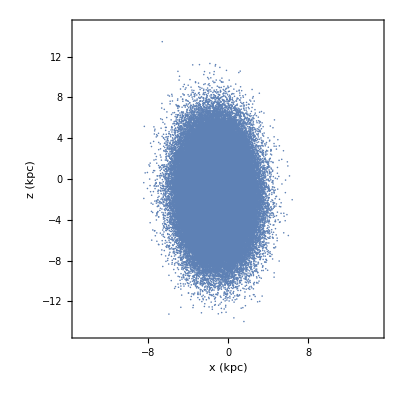
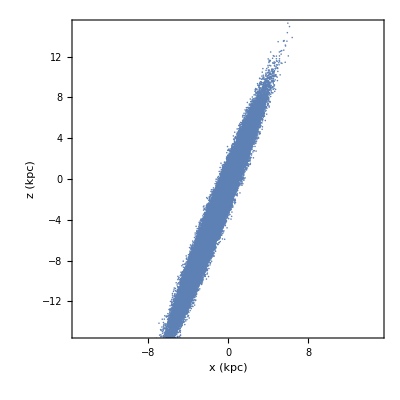
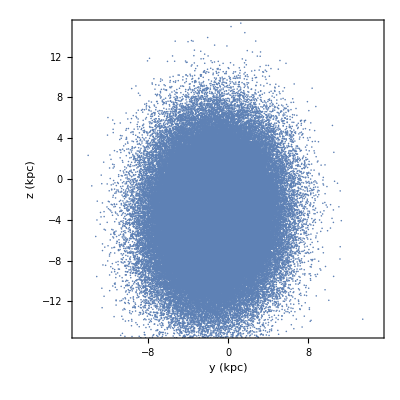

{-Graphics3D-}

```mathematica
checks=output⟦1⟧
dmDataMatrix=output⟦2⟧;
TableForm[dmDataMatrix⟦;;5⟧,TableHeadings->{None, tblHeadings},TableAlignments->"."]
coordListPlots2D=output⟦3⟧
coordListPlot3D=output⟦4⟧
```

# WIP